# Space ℙ_n

## Définition principale (Produit scalaire)

```mathematica
T:={1,2,3}
```

### Produit scalaire

```mathematica
⟨p_|q_⟩:=Sum[p q,{t,T}]
```

## Autres définitions

### La norme

```mathematica
norm[x_]:=√⟨x|x⟩
```

### Normalization d’un vecteur

```mathematica
normalize[x_]:=x/(√⟨x|x⟩)
```

### Normalization d’un ensemble de vecteur

```mathematica
normalizeListe[vectors_]:=Table[normalize[vectors[[i]]],{i,1,Length[vectors]}]
```

### La projection orthogonale de y sur x

```mathematica
projection[y_,x_]:=⟨x|y⟩x/⟨x|x⟩
```

### Orthogonalisation (Gram–Schmidt algorithm)

```mathematica
gramSchmidt[vectors_]:=Module[{oVectors=vectors},
Do[oVectors[[i]]-=projection[oVectors[[i]],oVectors[[j]]],{i,2,Length[vectors]},{j,1,i-1}];
oVectors]
```

### Matrice d’orthonormalité

```mathematica
orthogonality[vectors_]:=Table[⟨vectors[[i]]|vectors[[j]]⟩,{i,1,Length[vectors]},{j,1,Length[vectors]}]//Simplify//TableForm
```

## La base

### Base quelconque

La dimension de la base

```mathematica
dim:=3
```

```mathematica
baseQuelconque=Table[t^n,{n,1,dim}]
```

{t,t^2,t^3}

```mathematica
(*baseQuelconque=Table[Sin[n π x] ,{n,1,dim}]*)
```

```mathematica
orthogonality[baseQuelconque]
```

14 | 36 | 98
36 | 98 | 276
98 | 276 | 794

### Base orthogonale

```mathematica
baseOrthogonale=gramSchmidt[baseQuelconque]
```

{t,-(18 t)/7+t^2,-7 t+t^3-84/19 (-(18 t)/7+t^2)}

```mathematica
orthogonality[baseOrthogonale]
```

14 | 0 | 0
0 | 38/7 | 0
0 | 0 | 36/19

### Base orthonormale

```mathematica
baseOrthonormale=normalizeListe[baseOrthogonale]//Simplify
```

{t/(√14),(t (-18+7 t))/(√266),(t (83-84 t+19 t^2))/(6 √19)}

```mathematica
orthogonality[baseOrthonormale]
```

1 | 0 | 0
0 | 1 | 0
0 | 0 | 1

## Développement de P(t) sur une base

### La fonction à développer

```mathematica
P[t_] :=Sin[π/2 t]
```

### La base

```mathematica
base:=baseOrthonormale
```

### Les coéfficients

```mathematica
Subscript[c, n_]:=⟨base[[n]]|P[t] ⟩
```

```mathematica
Table[Subscript[c, n],{n,1,dim}]
```

{-√(2/7),-10 √(2/133),2/(√19)}

### Développement

```mathematica
Pdev[t]=∑_(n=1)^dim Subscript[c, n] base[[n]]
```

-t/7-10/133 t (-18+7 t)+1/57 t (83-84 t+19 t^2)

### Représentation

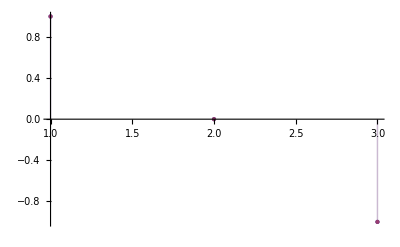

```mathematica
DiscretePlot[Evaluate[{P[t],Pdev[t]}],{t,T},PlotRange->All]
```

### Manipulation

```mathematica
Manipulate[DiscretePlot[Evaluate[{P[t],∑_(n=1)^N Subscript[c, n] base[[n]]}],{t,T},PlotRange->All],{N,1,dim,1},ControlType->Setter]
```